```mathematica
n = Input["Enter the number of pairs"]
pointlst = {}
pointlst1 = {}
parentlst = {}
childlst = {}
startlst = {}
endlst = {}
bendlst = {}
For[i=1, i≤n, i++,
pointlst1 = Join[pointlst1, {i}];
Print[pointlst1];
parentlst = Join[parentlst, {-1}];
childlst = Join[childlst, {{}}];
angles = Input["Enter angles of points of pair" ];
bend =Input["Enter the angle of bending for this pair"];
startlst = Join[startlst, {angles[[1]]}];
endlst = Join[endlst, {angles[[2]]}];
bendlst = Join[bendlst, {bend}];
pointlst = Join[pointlst, {{{Cos[angles[[1]]], Sin[angles[[1]]]}, {Cos[angles[[2]]], Sin[angles[[2]]]}, bend}}];
templst = pointlst1;
Print["Checkpoint 1"];
While[templst ≠{i},
Print["Checkpoint 2"];
temp = {templst[[1]]};
While[temp ≠ {},
Print["Checkpoint 3"];
If[angles[[1]] ≥ startlst[[temp[[1]]]]&&angles[[2]] ≤ endlst[[temp[[1]]]],
parentlst = ReplacePart[parentlst, i->temp[[1]]];
templst = DeleteElements[templst, temp];
Print[temp];
temp = childlst[[temp[[1]]]];
Print["End of Checkpoint 3"];,
Print[templst];
templst = DeleteElements[templst, temp];
Print[temp];
temp = DeleteElements[temp, {temp[[1]]}];
Print["End of Checkpoint 3"];];
]
];
If[parentlst[[i]] ≠ -1,
joined = Join[childlst[[parentlst[[i]]]], {i}];
childlst = ReplacePart[childlst, parentlst[[i]]->joined];
];
templst = pointlst1;
Print["Checkpoint 1"];
flag = -1;
For[j = 1, j<i, j++,
If[angles[[1]] ≤ startlst[[j]]&&angles[[2]] ≥ endlst[[j]],
flag = j;
Break;]
]
If[flag ≠ -1,
While[angles[[1]] ≤ startlst[[flag]]&&angles[[2]] ≥ endlst[[flag]],
flag = parentlst[[flag]];];
temp = childlst[[flag]];
k = Length[temp];
For[g = 1, g≤k, g++,
If[angles[[1]] ≤ startlst[[g]]&&angles[[2]] ≥ endlst[[g]],
joined = Join[childlst[[i]], {temp[[g]]}];
childlst = ReplacePart[childlst, i->joined];]]]]
childlst
parentlst
newchildlst = {}
For[i = 1, i≤n, i++,
tempchild = childlst[[i]];
Print[tempchild];
l = Length[tempchild];'
If[l>0,
tempnewchild  = {tempchild[[1]]};
If[l≥2,
For[j = 2, j≤l, j++,
k = j-1;
tempnewchild = Join[tempnewchild, {tempchild[[j]]}];
While[k>0 && startlst[[tempnewchild[[k]]]]≥ startlst[[tempchild[[j]]]],
tempnewchild = ReplacePart[tempnewchild, (k+1)->tempnewchild[[k]]];
k-=1;
];
rep = tempchild[[j]];
tempnewchild = ReplacePart[tempnewchild, k+1->rep];
];
];
newchildlst = Join[newchildlst, {tempnewchild}],
newchildlst = Join[newchildlst, {{}}]]
];
childlst = newchildlst
templst = pointlst1
newpointlst = {}
While[templst ≠ {},
Print["Wow1!"];
temp = templst[[1]];
While[parentlst[[temp]] ≠ -1,
temp = parentlst[[temp]]
];
queue = {temp};
While[queue ≠ {},
Print["Wow2!"];
temp = queue[[1]];
queue = DeleteElements[queue, {temp}];
templst = DeleteElements[templst, {temp}];
tempchild = childlst[[temp]];
l = Length[tempchild];
If[l>0,
For[i = 1, i≤l, i++,
queue = Join[queue, {tempchild[[i]]}];
If[i==1,
newpointlst = Join[newpointlst, {{{Cos[startlst[[temp]]], Sin[startlst[[temp]]]}, {Cos[startlst[[tempchild[[i]]]]], Sin[startlst[[tempchild[[i]]]]]}, bendlst[[temp]]}}],
newpointlst = Join[newpointlst, {{{Cos[endlst[[tempchild[[i-1]]]]], Sin[endlst[[tempchild[[i-1]]]]]}, {Cos[startlst[[tempchild[[i]]]]], Sin[startlst[[tempchild[[i]]]]]}, bendlst[[temp]]}}];
];
bendlst = ReplacePart[bendlst, tempchild[[i]]->bendlst[[tempchild[[i]]]]+bendlst[[temp]]];
];
newpointlst = Join[newpointlst, {{ {Cos[endlst[[tempchild[[l]]]]], Sin[endlst[[tempchild[[l]]]]]},{Cos[endlst[[temp]]], Sin[endlst[[temp]]]}, bendlst[[temp]]}}],
newpointlst = Join[newpointlst,  {{ {Cos[startlst[[temp]]], Sin[startlst[[temp]]]},{Cos[endlst[[temp]]], Sin[endlst[[temp]]]}, bendlst[[temp]]}}]
];
]
]
pointlst = newpointlst
```

1

{}

{}

{}

«4 more identical outputs»

{1}

Checkpoint 1

Checkpoint 1

{{}}

{-1}

{}

{}

{{}}

{1}

{}

Wow1!

Wow2!

{{{-1/2,(√3)/2},{-1,0},π/3}}

1



-Graphics-

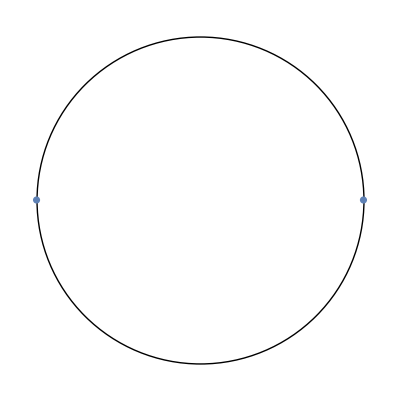

{}

{{-0.5,0.866025},{-0.59101,0.907061},{-0.688358,0.929198},{-0.788163,0.931554},{-0.886448,0.914035},{-0.979292,0.877338},{-1.063,0.822928},{-1.13422,0.752973},{-1.19013,0.670262},{-1.22849,0.578093},{-1.24777,0.48014},{-1.24721,0.380308},{-1.22683,0.282578},{-1.18744,0.190844},{-1.13061,0.108765},{-1.0586,0.0396134}}

FindFit::fitc: Number of coordinates (1) is not equal to the number of variables (2).

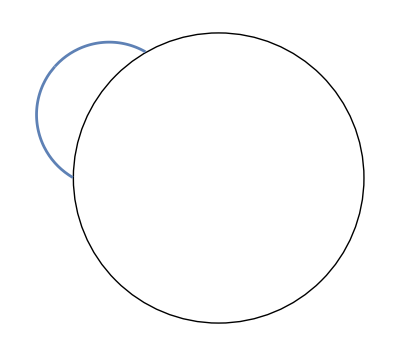

```mathematica
n = Length[pointlst]
circle = Graphics[Circle[{0, 0}, 1]]
points = ListPlot[{{-1, 0}, {1, 0}}]
Show[circle, points]
bent = {}
For[i = 1, i≤n, i++, 
p1 = pointlst[[i]][[1]][[1]]+I*pointlst[[i]][[1]][[2]];
p2 = pointlst[[i]][[2]][[1]]+I*pointlst[[i]][[2]][[2]];
k = Norm[p1+p2];
const = (-((2-k)/k)(p1+p2)+I(p2-p1))/(((2-k)/k)(p1+p2)+I(p2-p1));
c = Sqrt[1/(const((p1+p2)/2-I*const*(p1-p2)/2)-((p1+p2)(2-k)/(2k)-const(p1+p2)/k-I*const(p1-p2)/2))];
d = c*const;
a = (c(p1+p2)-I*d(p2-p1))/2;
b = ((c(p1+p2)(2-k)/(2k))+d((p1+p2)/k+I*(p2-p1)/2));
f =(a+b)/(c+d);
t = Tan[p];
theta  = pointlst[[i]][[3]];
theta =-theta;
m =Limit[Tan[w], w->theta, Direction->"FromAbove"];
If[theta == -Pi/2, x = (t^2-4)/((-t+2)^2);
y = 0, If[theta == Pi/2, x=(t^2-4)/((2+t)^2); y=0,
y =(t^2+(m*t)^2-4)/(t^2+((m*t)+2)^2);
x = 4*t/(t^2+((m*t)+2)^2)]];
point = x+I*y;
fpoint = (a*point+b)/(c*point+d);
If[-Pi/2≤-theta≤Pi/2,bent = Join[bent, {ParametricPlot[{Re[fpoint], Im[fpoint]}, {p, 0, Pi/2}, PlotStyle->Automatic]}];
pts = Table[{Re[fpoint], Im[fpoint]} /. p -> val, {val, 0, Pi/2, 0.1}];
Print[pts];
fit = FindFit[pts, (gi - g)^2 + (hi - h)^2 == o^2, {g, h, o}, {gi, hi}];
Graphics[{Circle[{g, h}, o]}],
bent = Join[bent,{ParametricPlot[{Re[fpoint],Im[fpoint]}, {p, Pi/2, Pi}, PlotStyle->Automatic]}]]]
Show[circle,bent,  PlotRange->Full]
```